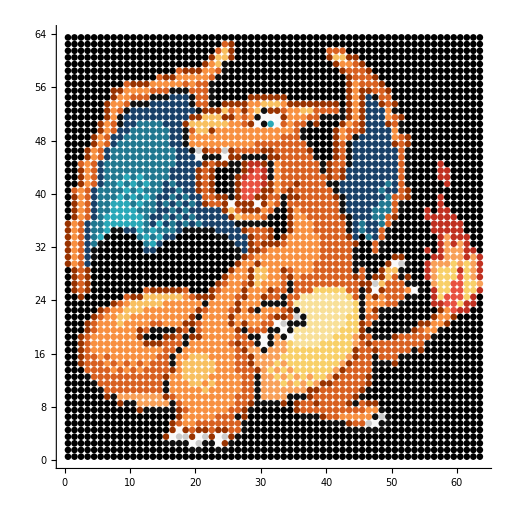

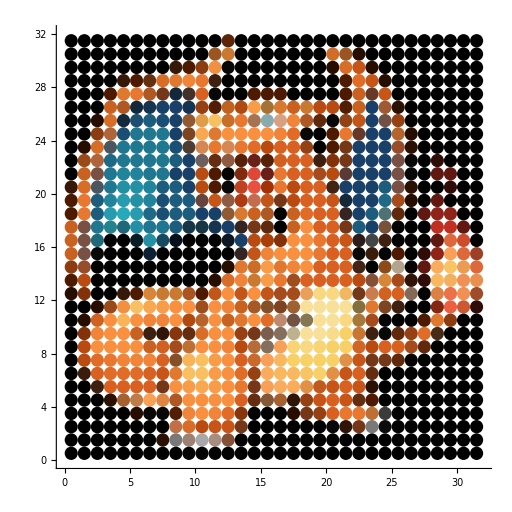

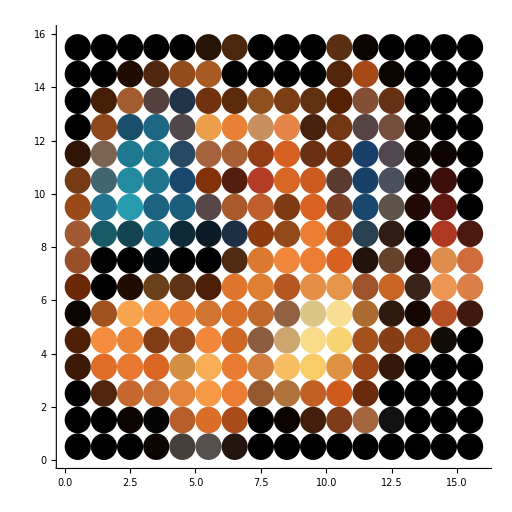

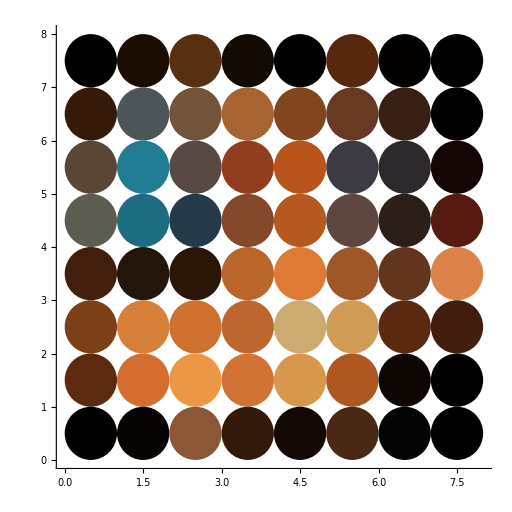

```mathematica
img = -Graphics-;

(* Color Data *)
imgColorDataSrc = ImageData[img];

imgColorData2=Table[0.0,{32},{32},{3}];
Table[Table[Table[imgColorData2[[(i/2)+0.5]][[(j/2)+0.5]][[k]]=
	((imgColorDataSrc[[i]][[j]][[k]]
+imgColorDataSrc[[i+1]][[j]][[k]]
+imgColorDataSrc[[i]][[j+1]][[k]]
+imgColorDataSrc[[i+1]][[j+1]][[k]])/4),
{k,1,3}],{j,1,64,2}],{i,1,64,2}];

imgColorData3=Table[0.0,{16},{16},{3}];
Table[Table[Table[imgColorData3[[(i/2)+0.5]][[(j/2)+0.5]][[k]]=
	((imgColorData2[[i]][[j]][[k]]
+imgColorData2[[i+1]][[j]][[k]]
+imgColorData2[[i]][[j+1]][[k]]
+imgColorData2[[i+1]][[j+1]][[k]])/4),
{k,1,3}],{j,1,32,2}],{i,1,32,2}];

imgColorData4=Table[0.0,{8},{8},{3}];
Table[Table[Table[imgColorData4[[(i/2)+0.5]][[(j/2)+0.5]][[k]]=
	((imgColorData3[[i]][[j]][[k]]
+imgColorData3[[i+1]][[j]][[k]]
+imgColorData3[[i]][[j+1]][[k]]
+imgColorData3[[i+1]][[j+1]][[k]])/4),
{k,1,3}],{j,1,16,2}],{i,1,16,2}];

(* Pixel Data *)
imgPixelData1 = 
Table[
Table[
{RGBColor[Table[imgColorDataSrc[[i]][[j]][[k]],{k,1,3}]],Disk[{j-0.5,65-i-0.5},0.5]},
{j,1,64}],
{i,1,64}];

imgPixelData2 = 
Table[
Table[
{RGBColor[Table[imgColorData2[[i]][[j]][[k]],{k,1,3}]],Disk[{j-0.5,33-i-0.5},0.5]},
{j,1,32}],
{i,1,32}];

imgPixelData3 = 
Table[
Table[
{RGBColor[Table[imgColorData3[[i]][[j]][[k]],{k,1,3}]],Disk[{j-0.5,17-i-0.5},0.5]},
{j,1,16}],
{i,1,16}];

imgPixelData4 = 
Table[
Table[
{RGBColor[Table[imgColorData4[[i]][[j]][[k]],{k,1,3}]],Disk[{j-0.5,9-i-0.5},0.5]},
{j,1,8}],
{i,1,8}];

(* Draw graphics *)
Graphics[
{
imgPixelData1
},
Axes->True,PlotRange->{{0,64},{0,64}},ImageSize->512]

Graphics[
{
imgPixelData2
},
Axes->True,PlotRange->{{0,32},{0,32}},ImageSize->512]

Graphics[
{
imgPixelData3
},
Axes->True,PlotRange->{{0,16},{0,16}},ImageSize->512]

Graphics[
{
imgPixelData4
},
Axes->True,PlotRange->{{0,8},{0,8}},ImageSize->512]
```